# Plot Seasonal Ricker Model EWS in rb

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Google\ Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_seasonal2"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=0;
bh=2.24;
```

## Import Data

```mathematica
rawEws=Import["data_export/ricker_trans_rb2/ews.csv"];
```

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
rawEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* Extract info *)
realNum=1;
seriesB = Cases[rawEws[[2;;,{1,2,3,4}]],{realNum,"Breeding",_,_}][[;;,{3,4}]];
seriesNB = Cases[rawEws[[2;;,{1,2,3,4}]],{realNum,"Non-breeding",_,_}][[;;,{3,4}]];
seriesTotal= Cases[rawEws[[2;;,{1,2,3,4}]],{realNum,"Total",_,_}][[;;,{3,4}]];
```

```mathematica
(* Useful info *)
tVals=seriesB[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
realMax=Max[rawEws[[;;,1]]][[1]];
```

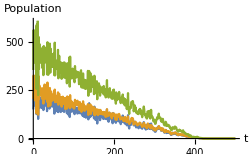

```mathematica
(* plot of breeding series *)
plotPop = ListPlot[{seriesB,seriesNB,seriesTotal},
Joined->True,
ImageSize->250,
LabelStyle->12,
AxesLabel->{"t","Population"},
PlotRange->{{0,tmax},{0,610}}]
```

## Bifurcation Diagram

### Output

```mathematica
rTicks
```

{-0.5,0.,0.5,1.,1.5,2.}

```mathematica
tbifVals=(rVals-bh)*tmax /(bl-bh);
```

```mathematica
rTicks=Range[bl,bh,0.5];
rTicksT=(rTicks-bh)*tmax/(bl-bh);
```

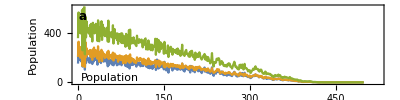

```mathematica
plotBifTraj=Show[{plotPop},
PlotRange->{{0,tmax*1.05},{-5,610}},
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Harvesting effort, F"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}]}
]
```

## EWS Plots

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

### Coefficient of variation

```mathematica
colCV=TMBcolours[[2]];
```

```mathematica
indexCV=Position[rawEws[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
cvSeriesB=Table[Cases[rawEws[[2;;,{1,2,3,indexCV}]],{rNum,"Breeding",_,_}][[;;,{3,4}]],{rNum,1,realMax}];
cvSeriesNB=Table[Cases[rawEws[[2;;,{1,2,3,indexCV}]],{rNum,"Non-breeding",_,_}][[;;,{3,4}]],{rNum,1,realMax}];
```

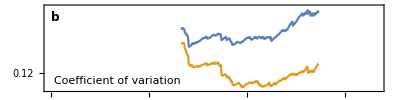

```mathematica
(* Plot EWS *)
ymin=0.1;
ymax=0.2;
plotVar=ListLinePlot[{cvSeriesB[[realNum]],cvSeriesNB[[realNum]]},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},{ymin,ymax}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Range[0,0.2,0.02],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["b",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}]
```

### Lag-1 AC

```mathematica
indexAC1=Position[rawEws[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
AC1SeriesB=Table[Cases[rawEws[[2;;,{1,2,3,indexAC1}]],{rNum,"Breeding",_,_}][[;;,{3,4}]],{rNum,1,realMax}];
AC1SeriesNB=Table[Cases[rawEws[[2;;,{1,2,3,indexAC1}]],{rNum,"Non-breeding",_,_}][[;;,{3,4}]],{rNum,1,realMax}];
```

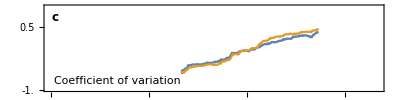

```mathematica
(* Plot EWS *)
ymin=-1;
ymax=1;
plotVar=ListLinePlot[{AC1SeriesB[[realNum]],AC1SeriesNB[[realNum]]},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},{ymin,ymax}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Range[-1,1,0.5],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}]
```

### Skewness

```mathematica
indexSkew=Position[rawEws[[1]],"Skewness"][[1,1]];
```

```mathematica
skewSeriesB=Table[Cases[rawEws[[2;;,{1,2,3,indexSkew}]],{rNum,"Breeding",_,_}][[;;,{3,4}]],{rNum,1,realMax}];
skewSeriesNB=Table[Cases[rawEws[[2;;,{1,2,3,indexSkew}]],{rNum,"Non-breeding",_,_}][[;;,{3,4}]],{rNum,1,realMax}];
```

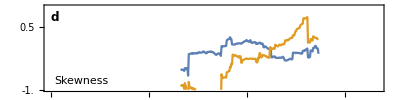

```mathematica
(* Plot EWS *)
ymin=-1;
ymax=1;
plotVar=ListLinePlot[{skewSeriesB[[realNum]],skewSeriesNB[[realNum]]},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},{ymin,ymax}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Range[-1,1,0.5],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["d",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Skewness",ls],textPos,{-1,0}]}]
```

### Kurtosis

```mathematica
indexKurt=Position[rawEws[[1]],"Kurtosis"][[1,1]];
```

```mathematica
kurtSeriesB=Table[Cases[rawEws[[2;;,{1,2,3,indexKurt}]],{rNum,"Breeding",_,_}][[;;,{3,4}]],{rNum,1,realMax}];
kurtSeriesNB=Table[Cases[rawEws[[2;;,{1,2,3,indexKurt}]],{rNum,"Non-breeding",_,_}][[;;,{3,4}]],{rNum,1,realMax}];
```

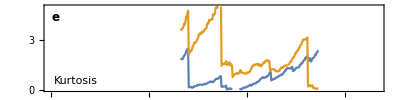

```mathematica
(* Plot EWS *)
ymin=0;
ymax=5;
plotVar=ListLinePlot[{kurtSeriesB[[realNum]],kurtSeriesNB[[realNum]]},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},{ymin,ymax}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
(*FrameTicks->{{Range[-1,1,0.5],Automatic},{Automatic,Automatic}}*)
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["e",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Kurtosis",ls],textPos,{-1,0}]}]
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

```mathematica
(* Function to compute Kendall tau *)
Clear[ktauComp]
ktauComp[series_]:=Module[{temp},
(* get rid of empty elements and transpose *)
temp=Transpose[DeleteCases[DeleteCases[series,{_,""}],{"",_}]];
(* compute Kendall tau *)
ktau=KendallTau[temp[[1]],temp[[2]]]
]
```

### Coefficient of variation

```mathematica
(* Compute kendall tau values *)
cvKtausB=Table[ktauComp[cvSeriesB[[rNum]]],{rNum,1,realMax}];
cvKtausNB=Table[ktauComp[cvSeriesNB[[rNum]]],{rNum,1,realMax}];
```

```mathematica
cvKtausB
```

{0.511171,0.105123,0.297675,0.257594}

```mathematica
(* Box plot *)
boxCV=BoxWhiskerChart[{cvKtausB,cvKtausNB},If[outliers,"Outliers"],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->{TMBcolours[[1]],TMBcolours[[2]]},
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### AIC weights - take ensemble of values at time 300

```mathematica
indexWhopf=Position[ewsBootFull[[1,1]],"AIC hopf"][[1,1]];
indexWfold=Position[ewsBootFull[[1,1]],"AIC fold"][[1,1]];
indexWnull=Position[ewsBootFull[[1,1]],"AIC null"][[1,1]];
```

```mathematica
tEval=299;
```

```mathematica
wHopfMeans=Table[Cases[ewsBootFull[[seed]][[;;,{1,2,indexWhopf}]],{_,"Mean",_}][[;;,{1,3}]],{seed,1,Length[ewsBootFull]}];
wFoldMeans=Table[Cases[ewsBootFull[[seed]][[;;,{1,2,indexWfold}]],{_,"Mean",_}][[;;,{1,3}]],{seed,1,Length[ewsBootFull]}];
wNullMeans=Table[Cases[ewsBootFull[[seed]][[;;,{1,2,indexWnull}]],{_,"Mean",_}][[;;,{1,3}]],{seed,1,Length[ewsBootFull]}];
```

```mathematica
(* AIC values at time tEval *)
wHopfEvals=Table[FirstCase[wHopfMeans[[seed]],{t_/;t>=tEval,_}],{seed,1,Length[ewsBootFull]}][[;;,2]];
wFoldEvals=Table[FirstCase[wFoldMeans[[seed]],{t_/;t>=tEval,_}],{seed,1,Length[ewsBootFull]}][[;;,2]];
wNullEvals=Table[FirstCase[wNullMeans[[seed]],{t_/;t>=tEval,_}],{seed,1,Length[ewsBootFull]}][[;;,2]];
```

```mathematica
(* Box plot *)
boxAic=BoxWhiskerChart[{wFoldEvals,wHopfEvals,wNullEvals},If[outliers,"Outliers"],
LabelStyle->ls,
PlotRange->{0,1},
ImageSize->imgsBox,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.25]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->aicCols,
ImagePadding->padBox,
Epilog->{
Text[Style["t=300",ls],ktauTextPos,{-1,0}],
Text[Style["j",labelLetterPosSize,Bold],labelLetterPosBox]}
]
```

-Graphics-

## Power Spectrum Plot

### Colour function

```mathematica
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Power Spectrum of original series

```mathematica
specData//Dimensions
```

{493,3}

```mathematica
specData[[1]]
```

{Time,Frequency,Empirical}

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[specData[[2;;,1]]][[1;;;;4]]
```

{199.,279.,359.}

```mathematica
(* Organise list of power spectra *)
pspecs=Table[
Cases[specData,
{i,_,_}]⟦;;,{2,3}⟧,
{i,plotTimes}];
```

```mathematica
pspecs//Dimensions
```

{3,41,2}

```mathematica
timeRange
```

{199.,359.}

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{colFun1[(#-199)/(419-199)]&,timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

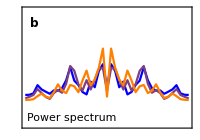

```mathematica
plotPspec=ListLinePlot[pspecs,
PlotRange->{-0.007,0.03},
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Range[0,0.03,0.01]},{None,Range[-3,3,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.82,0.75}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.5cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+4*heightEws+heightBif+4*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotAIC,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxAic,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotAC,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxAc,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotSmax,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSmax,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th (top) row  *)
Inset[Show[plotBifTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspec,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

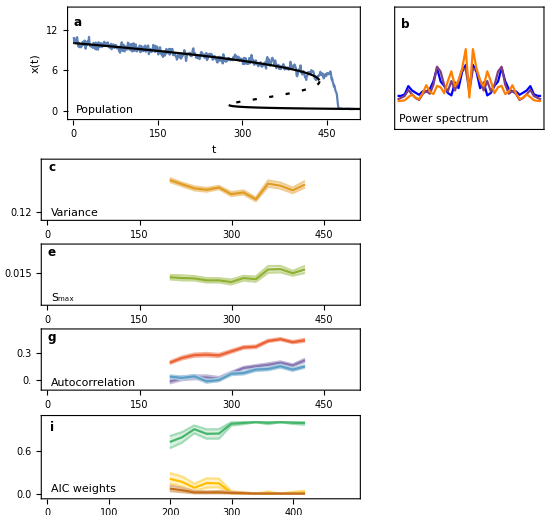

```mathematica
plotGrid
```

```mathematica
(*Export["figures/fig_ews_fold.png",plotGrid,ImageResolution->400];*)
```